```mathematica
Clear["Global`*"]
```

```mathematica
r=1000.;(*radius of curvature [mm]*)
d=60.;(*mirror diameter [mm]*)
l1=195.;(*distance between source and mirror [mm]*)
l2=185.;(*distance between mirror and detector [mm]*)
L=60.;(*length of the source [mm]*)
ψ=2ArcSin[d/(2r)];(*mirror apex angle*)
λ0 = 0.162;(*nm*)
α0=L^2/(16 l1^2)Sin[ψ]/(1-d/(2l1));
φ0=(L+d)/(2l1);
θ0 =0.003737816423136225;
```

```mathematica
RefrIndexes=Drop[Import[#,"Table"],2]&/@FileNames["RefrIndex*.txt",NotebookDirectory[]];
{δAl2O3,δAu,δSi,δW46Ru37B17}=Interpolation[#[[All,{1,2}]],Method->"Spline"]&/@RefrIndexes;
{γAl2O3,γAu,γSi,γW46Ru37B17}=Interpolation[#[[All,{1,3}]],Method->"Spline"]&/@RefrIndexes;
```

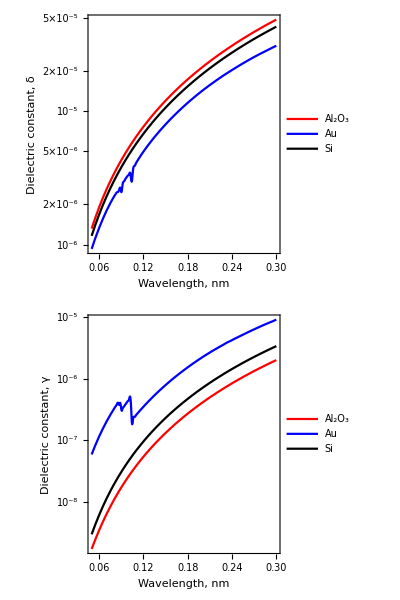

```mathematica
Grid[{{Plot[#[x]&/@{δAl2O3,δAu,δSi}//Evaluate,{x,0.05,0.3},ScalingFunctions->"Log",PlotStyle->{Red,Blue,Black},ImageSize->{400,300},GridLines->{Range[0.06,0.3,0.02],{10^-6,2.5 10^-6,5 10^-6,10^-5,2.5 10^-5,5 10^-5}},Frame->True,FrameLabel->(Style[#,Black,22,Bold]&/@{"Wavelength, nm","Dielectric constant, δ"}),FrameTicks->{{{{10^-6,"10^-6"},{2.5 10^-6,""},{5 10^-6,""},{10^-5,"10^-5"},{2.5 10^-5,""},{5 10^-5,""}},None},{Automatic,None}},PlotLegends->Placed[LineLegend[Style[#,Black,22,Bold]&/@{"Al_2O_3","Au","Si"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.8,0.3}],FrameTicksStyle->Directive[Black,22],FrameStyle->Bold,AspectRatio->1/1.5]},{
Plot[#[x]&/@{γAl2O3,γAu,γSi}//Evaluate,{x,0.05,0.3},ScalingFunctions->"Log",PlotStyle->{Red,Blue,Black},ImageSize->{400,300},GridLines->{Range[0.06,0.3,0.02],{10^-8,10^-7,10^-6,10^-5}},Frame->True,FrameLabel->(Style[#,Black,22,Bold]&/@{"Wavelength, nm","Dielectric constant, γ"}),PlotLegends->Placed[LineLegend[Style[#,Black,22,Bold]&/@{"Al_2O_3","Au","Si"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.8,0.3}],FrameTicksStyle->Directive[Black,22],FrameStyle->Bold]}},Spacings->{1,0}]
```

```mathematica
Rf[θ_,εε_]:=Abs[Cos[θ+ArcSin[Cos[θ]/√εε]]/Cos[θ-ArcSin[Cos[θ]/√εε]]]^2
```

```mathematica
εAl2O3[λ_]:=1-δAl2O3[λ]+ⅈ γAl2O3[λ]
εAu[λ_]:=1-δAu[λ]+ⅈ γAu[λ]
εSi[λ_]:=1-δSi[λ]+ⅈ γSi[λ]
εW46Ru37B17[λ_]:=1-δW46Ru37B17[λ]+ⅈ γW46Ru37B17[λ]
```

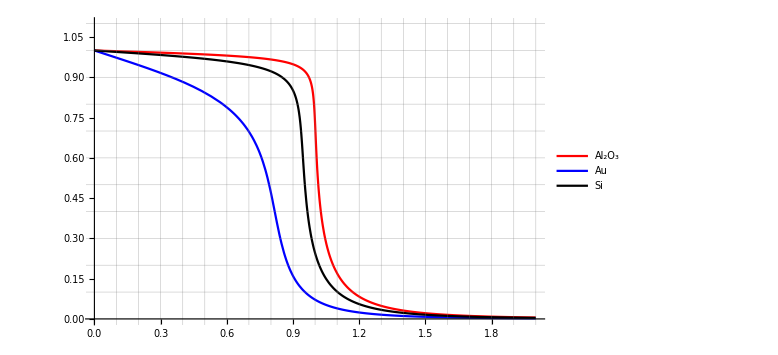
-Graphics-Angle / θ_crit Al_2O_3Reflectivity

```mathematica
Labeled[Plot[Rf[x θ0,#[λ0]]&/@{εAl2O3,εAu,εSi}//Evaluate,{x,0,2},PlotStyle->{Red,Blue,Black},ImageSize->Large,GridLines->All,TicksStyle->Directive[Black, 14,Bold],PlotLegends->Placed[LineLegend[Style[#,Black,16,Bold]&/@{"Al_2O_3","Au","Si"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{Right,Center}],AxesStyle->Bold,PlotRange->{{0,2},{0,1.1}}],(Style[#,Black,16,Bold,FontFamily->"Arabic Transparent"]&/@{"Angle / θ_crit Al_2O_3","Reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]
```

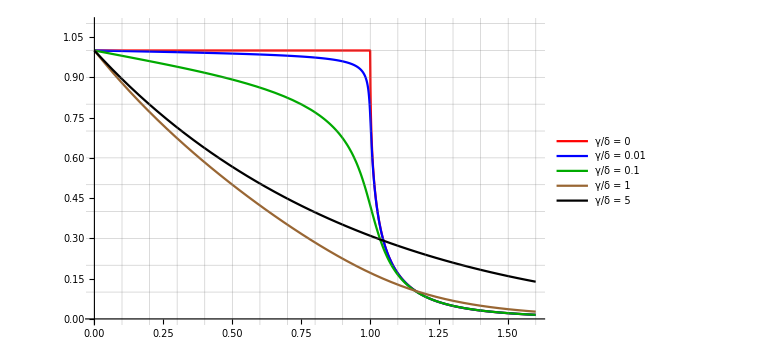
-Graphics-Angle / θ_critReflectivity

```mathematica
Labeled[Plot[Rf[x θ0,#]&/@({1-#,1-#+ⅈ 0.01#,1-#+ⅈ 0.1#,1-#+ⅈ#,1-#+ⅈ 5#}&@δAl2O3[λ0])//Evaluate,{x,0,1.6},Exclusions->None,PlotStyle->{Red,Blue,Darker[Green],Brown,Black},GridLines->All,TicksStyle->Directive[14,Black,Bold],ImageSize->Large,PlotLegends->Placed[LineLegend[Style[#,Black,16,Bold]&/@{"γ/δ = 0","γ/δ = 0.01","γ/δ = 0.1","γ/δ = 1","γ/δ = 5"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{Right,Center}],AxesStyle->Bold,PlotRange->{{0,1.6},{0,1.1}}],(Style[#,Black,16,Bold,FontFamily->"Arabic Transparent"]&/@{"Angle / θ_crit","Reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]
```

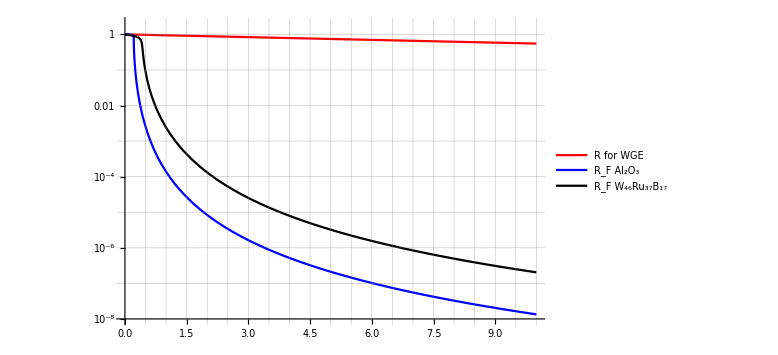
-Graphics-Angle, °Reflectivity

```mathematica
R[ψ_,γ_,δ_]:=Exp[-ψ γ/δ^(3/2)]
Labeled[Plot[{R@@{x °,γAl2O3[λ0], δAl2O3[λ0]},Rf[x °,#[λ0]]&/@{εAl2O3,εW46Ru37B17}}//Evaluate,{x,0,10},ScalingFunctions->"Log",PlotStyle->{Red,Blue,Black},ImageSize->Large,GridLines->All,TicksStyle->Directive[20,Black,Bold],PlotLegends->Placed[LineLegend[Style[#,Black,22,Bold]&/@{"R for WGE","R_F Al_2O_3","R_F W_46Ru_37B_17"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{Right,Center}],PlotRange->{{0,10},{10^-8,2}},AxesStyle->Bold],(Style[#,Black,22,Bold,FontFamily->"Arabic Transparent"]&/@{"Angle, °","Reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]
```

```mathematica
TIS[θ0_,ε_,λ_,σ_]:=Rf[θ0,ε](1-Exp[-((4π σ Sin[θ0])/λ)^2])
Rs[θ0_,ε_,λ_,σ_]:=Rf[θ0,ε]Exp[-((4π σ Sin[θ0])/λ)^2]
```

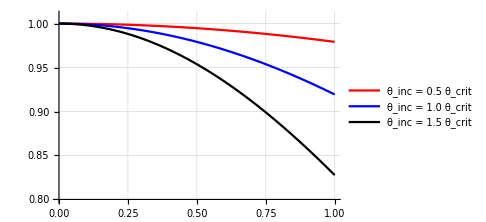
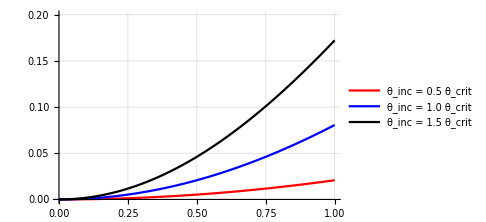
-Graphics-Spec Reflectivity
-Graphics-TISRMS height σ, nm

```mathematica
Labeled[
Grid[
{
{
Labeled[
Plot[Rs[# θ0,εAl2O3[λ0],λ0,x]/Rf[# θ0, εAl2O3[λ0]]&/@{0.5,1,1.5}//Evaluate,{x,0,1},ImageSize->Medium,PlotStyle->{Red,Blue,Black},GridLines->Automatic,TicksStyle->Directive[20,Black,Bold],PlotLegends->Placed[LineLegend[Style[#,Black,18,Bold]&/@{"θ_inc = 0.5 θ_crit","θ_inc = 1.0 θ_crit","θ_inc = 1.5 θ_crit"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.35}],PlotRange->{{0,1},{0.8,1.01}},AxesStyle->Bold]
,Style[#,Black,22,Bold,FontFamily->"Arabic Transparent"]&@"Spec Reflectivity",Left,RotateLabel->True,ImageMargins->3]},
{
Labeled[
Plot[TIS[# θ0,εAl2O3[λ0],λ0,x]/Rf[# θ0, εAl2O3[λ0]]&/@{0.5,1,1.5}//Evaluate,{x,0,1},ImageSize->Medium,PlotStyle->{Red,Blue,Black},GridLines->Automatic,TicksStyle->Directive[20,Black,Bold],PlotLegends->Placed[LineLegend[Style[#,Black,18,Bold]&/@{"θ_inc = 0.5 θ_crit","θ_inc = 1.0 θ_crit","θ_inc = 1.5 θ_crit"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.65}],PlotRange->{{0,1},{0,0.2}},AxesStyle->Bold]
,Style[#,Black,22,Bold,FontFamily->"Arabic Transparent"]&@"TIS",Left,RotateLabel->True,ImageMargins->3]
}
},Spacings->{2,0}]
,(Style[#,Black,22,Bold,FontFamily->"Arabic Transparent"]&@"RMS height σ, nm"),Bottom]
```

```mathematica
SurfaceVal=-0.049Import[FileNames["80x80um.txt",NotebookDirectory[]][[1]],"Table"][[17;;]];
σ=Mean[RootMeanSquare[SurfaceVal]];
PSDAl2O3=Mean[80/512 Abs[Fourier[ SurfaceVal[[#]] 10^-3]//Drop[#,-Length[#]/2]&]^2&/@Range[512]];
PSDm=NonlinearModelFit[{Range[1/80,511/80,1/40],PSDAl2O3}//Transpose,2/(√π)Gamma[1/2+αα]/Gamma[αα](σ^2 ξξ 10^-6)/((1+x^2 ξξ^2)^(1/2+αα)),{αα,ξξ},x];
{α,ξ}={αα,ξξ}/.PSDm["BestFitParameters"];
```

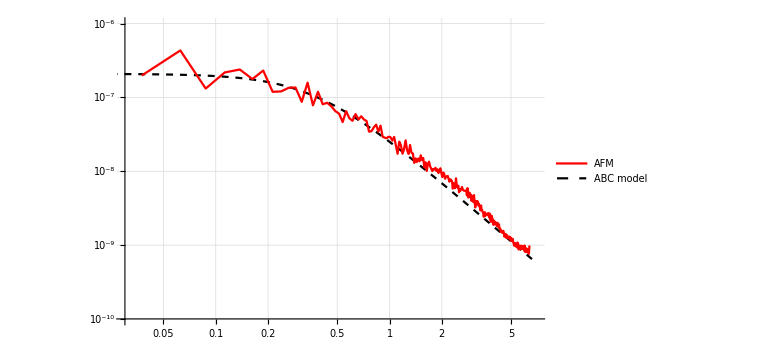
-Graphics-Spatial frequence, μm^-1PSD-function, μm^3

```mathematica
Labeled[Show[Plot[PSDm[x],{x,0,7},ScalingFunctions->{"Log","Log"},PlotRange->{{0.03,7},{10^-10,10^-6}},PlotStyle->Directive[Black,Dashed],PlotLegends->Placed[LineLegend[{Red,Directive[Black,Dashed]},Style[#,Black,16,Bold]&/@{"AFM","ABC model"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.2,0.3}],GridLines->Full],ListPlot[{Range[3/80,511/80,1/40],Drop[PSDAl2O3,1]}//Transpose,PlotStyle->Red,ScalingFunctions->{"Log","Log"},Joined->True],AxesStyle->Bold,TicksStyle->Directive[16,Black,Bold],ImageSize->Large],(Style[#,Black,16,Bold,FontFamily->"Arabic Transparent"]&/@{"Spatial frequence, μm^-1","PSD-function, μm^3"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]
```

```mathematica
PSD1D[p_,α_,ξ_,σ_]:=2/(√π)Gamma[1/2+α]/Gamma[α](σ^2 ξ 10^-6)/((1+p^2 ξ^2)^(1/2+α))
PSD2D[νx_,νy_,α_,ξ_,σ_]:=(10^-6 σ^2 ξ^2 α)/(π(1+(νx^2+νy^2)ξ^2)^(1+α))

t[θ_,λ_]:=(2 Sin[θ])/(Sin[θ]+√(εAl2O3[λ]-Cos[θ]^2))
k[λ_]:=(2π)/λ
P[θ_,θ0_,λ_]:=(k[λ]^3 Abs[1-εAl2O3[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/(16π Sin[θ0])10^9 PSD1D[1/(λ 10^-3)Abs[Cos[θ0]-Cos[θ]],α,ξ,σ]
F[θ_,φ_,θ0_,λ_]:=(k[λ]^4 Abs[1-εAl2O3[λ]]^2 Abs[t[θ,λ]t[θ0,λ]]^2)/((4π)^2 Sin[θ0])10^12 PSD2D[1/(λ 10^-3)(Cos[θ]Cos[φ]-Cos[θ0]),1/(λ 10^-3)Cos[θ]Sin[φ],α,ξ,σ]
AP[θinc_,λ_]:=AP[θinc,λ]=NIntegrate[P[θ,θinc,λ],{θ,0,θ0,θinc,π/2}]
AF[θinc_,λ_]:=AF[θinc,λ]=NIntegrate[F[θsc,φsc,θinc,λ]Cos[θsc],{θsc,0,θ0,θinc,π/2},{φsc,-π,π}]
Π[θ_,θ0_,λ_]:=P[θ,θ0,λ]/AP[θ0,λ]
Φ[θ_,φ_,θ0_,λ_]:=F[θ,φ,θ0,λ]/AF[θ0,λ]
```

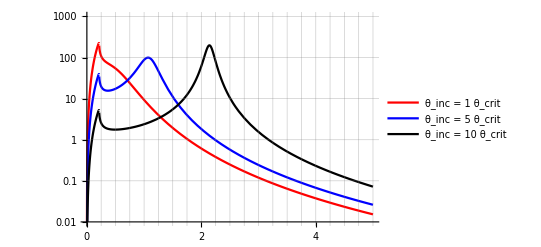
-Graphics- | -Graphics-
-Graphics-Angle θ, °Indicatrix | -Graphics3D-Indicatrix

```mathematica
Grid[{
{
Graphics[Text[Style["a)",18,Bold,Black],Scaled[{-70,0}]],ImageSize->{500,30}],
Graphics[Text[Style["b)",18,Bold,Black],Scaled[{-70,0}]],ImageSize->{500,30}]
},
{
Labeled[Plot[Π[x °,# θ0,λ0]&/@{1,5,10}//Evaluate,{x,0,5},ImageSize->{400,250},PlotStyle->{Red,Blue,Black},TicksStyle->Directive[16,Black,Bold],AxesStyle->Bold,ScalingFunctions->"Log",GridLines->{All,Automatic},PlotRange->{{0,5},{10^-2,10^3}},PlotLegends->Placed[LineLegend[Style[#,Black,16,Bold]&/@{"θ_inc = 1 θ_crit","θ_inc = 5 θ_crit","θ_inc = 10 θ_crit"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.77,0.7}],Ticks->{{{0,"0"},{0.25,""},{0.5,""},{0.75,""},{1,"1"},{1.25,""},{1.5,""},{1.75,""},{2,"2"},{2.25,""},{2.5,""},{2.75,""},{3,"3"},{3.25,""},{3.5,""},{3.75,""},{4,"4"},{4.25,""},{4.5,""},{4.75,""},{5,"5"}},Automatic}],(Style[#,Black,18,Bold,FontFamily->"Arabic Transparent"]&/@{"Angle θ, °","Indicatrix"}),{Bottom,Left},RotateLabel->True], 
Labeled[Plot3D[Φ[θ °,φ °,10θ0,λ0],{θ,0.1,6},{φ,-0.1,0.1},ScalingFunctions->"Log",ColorFunction->Function[{x,y,z},Hue[0.7(1-z),1,0.85]],TicksStyle->Directive[16,Black,Bold],AxesLabel->(Style[#,18,Bold,Black]&/@{"θ, °","φ, °"}),PlotPoints->50,ImageSize->{400,300},Ticks->{Automatic,Automatic,{{10^1,""},{10^2,"10^2"},{10^3,""},{10^4,"10^4"},{10^5,""},{10^6,"10^6"}}}],Style[#,Black,18,Bold,FontFamily->"Arabic Transparent"]&@"Indicatrix",Top,FrameMargins->4]
}
}]
```

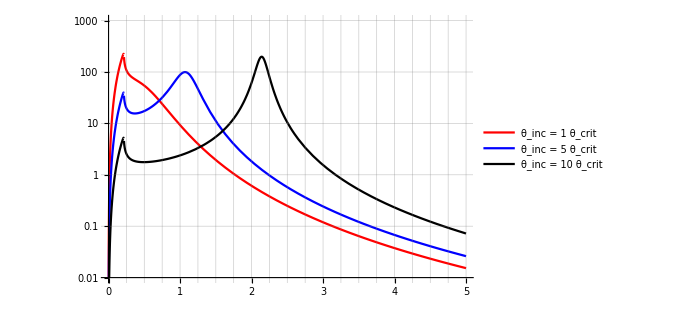
-Graphics-Angle θ, °Indicatrix 1D
-Graphics3D-Indicatrix 2D

```mathematica
Grid[{
{
Labeled[Plot[Π[x °,# θ0,λ0]&/@{1,5,10}//Evaluate,{x,0,5},ImageSize->{500,250},PlotStyle->{Red,Blue,Black},TicksStyle->Directive[20,Black,Bold],AxesStyle->Bold,ScalingFunctions->"Log",GridLines->{All,Automatic},PlotRange->{{0,5},{10^-2,10^3}},PlotLegends->Placed[LineLegend[Style[#,Black,16,Bold]&/@{"θ_inc = 1 θ_crit","θ_inc = 5 θ_crit","θ_inc = 10 θ_crit"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.77,0.7}],Ticks->{{{0,"0"},{0.25,""},{0.5,""},{0.75,""},{1,"1"},{1.25,""},{1.5,""},{1.75,""},{2,"2"},{2.25,""},{2.5,""},{2.75,""},{3,"3"},{3.25,""},{3.5,""},{3.75,""},{4,"4"},{4.25,""},{4.5,""},{4.75,""},{5,"5"}},Automatic}],(Style[#,Black,22,Bold,FontFamily->"Arabic Transparent"]&/@{"Angle θ, °","Indicatrix 1D"}),{Bottom,Top},RotateLabel->True]
},
{ 
Labeled[Plot3D[Φ[θ °,φ °,10θ0,λ0],{θ,0.1,6},{φ,-0.1,0.1},ScalingFunctions->"Log",ColorFunction->Function[{x,y,z},Hue[0.7(1-z),1,0.85]],TicksStyle->Directive[20,Black,Bold],AxesLabel->(Style[#,22,Bold,Black]&/@{"θ, °","φ, °"}),PlotPoints->50,ImageSize->{500,300},Ticks->{Automatic,Automatic,{{10^1,""},{10^2,"10^2"},{10^3,""},{10^4,"10^4"},{10^5,""},{10^6,"10^6"}}}],Style[#,Black,22,Bold,FontFamily->"Arabic Transparent"]&@"Indicatrix 2D",Top,FrameMargins->4]
}
}]
```

```mathematica
Clear[R,AR]
```

```mathematica
angles=Import[NotebookDirectory[]<>"angles_plane2D.mx"];
anglist=Prepend[Transpose[{MovingAverage[#[[1]]/θ0,2],#[[2]]}]&@HistogramList[angles,{0.008°},"PDF"],{0.,0.}];
```

```mathematica
R[θ_,ψ_,λ_]:=Rf[θ,εAl2O3[λ]]^(Quotient[ψ,2θ]+1)
AR=Quiet[NIntegrate[θ R[θ,ψ,λ0],{θ,0,θ0,π/2.}]];
```

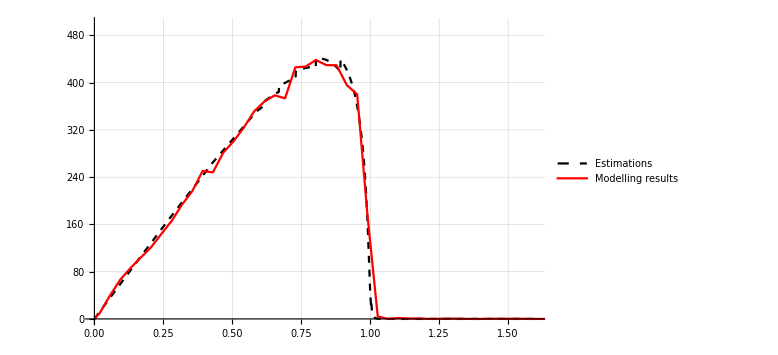
-Graphics-θ_inc / θ_critРаспределение

```mathematica
Labeled[
Show[
Plot[x θ0 R[x θ0,ψ,λ0]/AR,{x,0,1.6},Exclusions->None,PlotRange->{{0,1.6},{0,500}},PlotStyle->Directive[Black,Dashed],GridLines->Full,PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Red},Style[#,Black,16,Italic]&/@{"Estimations","Modelling results"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.8,0.8}]],
ListPlot[anglist,Joined->True,PlotStyle->Red,PlotRange->{{0,1.6},{0,500}}]
,TicksStyle->Directive[20,Black],ImageSize->Large]
,(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"θ_inc / θ_crit","Распределение"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]
```

```mathematica
Export["D:\\OneDrive\\Научная деятельность\\Диплом\\fig4.svg",Labeled[
Show[
Plot[x θ0 R[x θ0,ψ,λ0]/AR,{x,0,1.6},Exclusions->None,PlotRange->{{0,1.6},{0,500}},PlotStyle->Directive[Black,Dashed],GridLines->Full,PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Red},Style[#,Black,16,Italic]&/@{"Estimations","Modelling results"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.8,0.8}]],
ListPlot[anglist,Joined->True,PlotStyle->Red,PlotRange->{{0,1.6},{0,500}}]
,TicksStyle->Directive[20,Black],ImageSize->Large]
,(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"θ_inc / θ_crit","Распределение"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]]
```

D:\OneDrive\Научная деятельность\Диплом\fig4.svg

```mathematica
Iimp[h_,r_]:=If[h==0,1,2/θ0^2(1/2 θ0 √(θ0^2-2 h/r)-h/r Log[θ0+√(θ0^2-2 h/r)]+h/(2r)Log[2 h/r])]
Imp[x_,ImpH_,ImpR_:10r(1-Cos[2/3θ0])]:=Piecewise[{{√(((ImpH^2+ImpR^2)/(2ImpH))^2-x^2)-(ImpR^2-ImpH^2)/(2ImpH),-ImpR<x<ImpR}}]
Timp[ImpH_,r_,ImpR_:10r(1-Cos[2/3θ0])]:=Timp[ImpH,r,ImpR]=Re[NIntegrate[Iimp[Imp[x,ImpH,ImpR],r]/2/ImpR,{x,-ImpR,ImpR}]]
```

```mathematica
resscat[res_]:=Select[res,#[[3]]==1&]
resspec[res_]:=Select[res,#[[3]]==0&]
detpts[res_]:=res[[All,1,{1,3}]]
```

```mathematica
r1000=Import[NotebookDirectory[]<>"results/ImpH_Series_R_1000.mx"];
r750=Import[NotebookDirectory[]<>"results/ImpH_Series_R_750.mx"];
r750new=Import[NotebookDirectory[]<>"results/ImpH_Series_R_750_new.mx"];
r500=Import[NotebookDirectory[]<>"results/ImpH_Series_R_500.mx"];
imph=1000r(1-Cos[2/3θ0])Join[Range[0,2,0.25],Range[2.5,6,0.5],Range[7,8]];
```

```mathematica
T[detpts_,size_:10r(1-Cos[2/3θ0])]:=Length[Select[detpts[[All,1]],Abs[#]<size&]]
TList[r_,n_,ImpR_:10r(1-Cos[2/3θ0])]:=Prepend[{1000#,Timp[#,r,ImpR]}&/@Drop[Range[0,0.025,0.025/n],1],{0.,1.}]
ResTList[res_]:=ResTList[res]=Transpose[{imph,#/Max@#&@(T/@(detpts/@res))}]
```

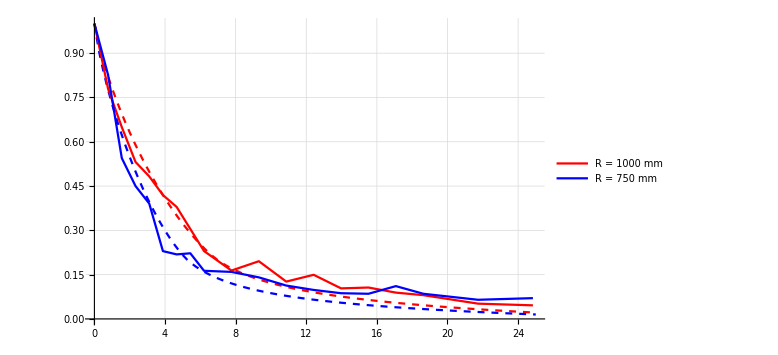
-Graphics-Высота дефекта, мкмКоэффициент прохождения

```mathematica
Labeled[Show[ListPlot[Evaluate[TList[# r,100]&/@{1,0.75}],Joined->True,PlotRange->{{0,25},{0,1}},PlotStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]},GridLines->Full,PlotLegends->Placed[LineLegend[{Red,Blue},Style[#,Black,18,Italic]&/@{"R = 1 м","R = 0.75 м"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.7,0.7}]],ListPlot[Evaluate[ResTList/@{r1000,Join[r750new,r750,2]}],Joined->True,PlotStyle->{Red,Blue}],TicksStyle->Directive[20,Black],ImageSize->Large],(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"Высота дефекта, мкм","Коэффициент прохождения"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]
```

```mathematica
Export["D:\\OneDrive\\Научная деятельность\\Статья\\Вестник МГУ\\Рисунки\\fig6.svg",Labeled[Show[ListPlot[Evaluate[TList[# r,100]&/@{1,0.75}],Joined->True,PlotRange->{{0,25},{0,1}},PlotStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]},GridLines->Full,PlotLegends->Placed[LineLegend[{Red,Blue},Style[#,Black,18,Italic]&/@{"R = 1 м","R = 0.75 м"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.7,0.7}]],ListPlot[Evaluate[ResTList/@{r1000,Join[r750new,r750,2]}],Joined->True,PlotStyle->{Red,Blue}],TicksStyle->Directive[20,Black],ImageSize->Large],(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"Высота дефекта, мкм","Коэффициент прохождения"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]]
 Export["D:\\OneDrive\\Научная деятельность\\Статья\\Applied Physics Letters\\Figures\\fig6.svg",Labeled[Show[ListPlot[Evaluate[TList[# r,100]&/@{1,0.75}],Joined->True,PlotRange->{{0,25},{0,1}},PlotStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]},GridLines->Full,PlotLegends->Placed[LineLegend[{Red,Blue},Style[#,Black,18,Italic]&/@{"R = 1 m","R = 0.75 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.7,0.7}]],ListPlot[Evaluate[ResTList/@{r1000,Join[r750new,r750,2]}],Joined->True,PlotStyle->{Red,Blue}],TicksStyle->Directive[20,Black],ImageSize->Large],(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"defect height, μm","relative transmittance"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]]
```

D:\OneDrive\Научная деятельность\Статья\Вестник МГУ\Рисунки\fig6.svg

D:\OneDrive\Научная деятельность\Статья\Applied Physics Letters\Figures\fig6.svg

```mathematica
dimp=20r(1-Cos[2/3θ0]);
```

```mathematica
reshmin=Import[NotebookDirectory[]<>"results/ImpH_975nm_R_1000.mx"];
```

```mathematica
Export["D:\\OneDrive\\Научная деятельность\\Статья\\Applied Physics Letters\\Figures\\fig7_1.svg",DensityHistogram[Select[detpts[reshmin],-1<#[[1]]<1&&4<#[[2]]<6&],{dimp/2},FrameTicksStyle->Directive[Black,22],ColorFunction->(Hue[0.7(1-#),1,0.85]&),GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","z-coordinate, mm"}),ImageSize->Large,PlotRange->{{-1,1},{4,6}}]]
```

D:\OneDrive\Научная деятельность\Статья\Applied Physics Letters\Figures\fig7_1.svg

```mathematica
Export["D:\\OneDrive\\Научная деятельность\\Статья\\Вестник МГУ\\Рисунки\\fig7_1.svg",DensityHistogram[Select[detpts[reshmin],-1<#[[1]]<1&&4<#[[2]]<6&],{dimp/2},FrameTicksStyle->Directive[Black,22],ColorFunction->(Hue[0.7(1-#),1,0.85]&),GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-координата, мм","z-координата, мм"}),ImageSize->Large,PlotRange->{{-1,1},{4,6}}]]
```

D:\OneDrive\Научная деятельность\Статья\Вестник МГУ\Рисунки\fig7_1.svg

```mathematica
Export["D:\\OneDrive\\Научная деятельность\\Статья\\Applied Physics Letters\\Figures\\fig7_2.svg",Labeled[Show[ListPlot[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[detpts[reshmin][[All,1]],{Range[dimp/2-Quotient[δbeam[r,d,θ0]/2,dimp]dimp,dimp/2+Quotient[δbeam[r,d,θ0]/2,dimp]dimp,dimp]}],Joined->True,PlotRange->{{-1,1},{0,420}},PlotStyle->Red,GridLines->All,PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Red},Style[#,Black,18,Italic]&/@{"Estimations","Modelling results"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.74,0.25}]],Plot[I0[Length@reshmin,dimp]Iimp[Imp[x,hmin[σn[Length@reshmin,dimp]]]],{x,-2,2},Exclusions->None,PlotPoints->100,PlotStyle->Directive[Black,Dashed]],TicksStyle->Directive[20,Black],ImageSize->Large,AxesOrigin->{-1,0}],(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"x-coordinate, mm","Intensity"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]]
```

D:\OneDrive\Научная деятельность\Статья\Applied Physics Letters\Figures\fig7_2.svg

```mathematica
Export["D:\\OneDrive\\Научная деятельность\\Статья\\Вестник МГУ\\Рисунки\\fig7_2.svg",Labeled[Show[ListPlot[Transpose[{MovingAverage[#[[1]],2],#[[2]]}]&@HistogramList[detpts[reshmin][[All,1]],{Range[dimp/2-Quotient[δbeam[r,d,θ0]/2,dimp]dimp,dimp/2+Quotient[δbeam[r,d,θ0]/2,dimp]dimp,dimp]}],Joined->True,PlotRange->{{-1,1},{0,420}},PlotStyle->Red,GridLines->All,PlotLegends->Placed[LineLegend[{Directive[Black,Dashed],Red},Style[#,Black,18,Italic]&/@{"Теория","Результаты моделирования"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.74,0.25}]],Plot[I0[Length@reshmin,dimp]Iimp[Imp[x,hmin[σn[Length@reshmin,dimp]]]],{x,-2,2},Exclusions->None,PlotPoints->100,PlotStyle->Directive[Black,Dashed]],TicksStyle->Directive[20,Black],ImageSize->Large,AxesOrigin->{-1,0}],(Style[#,Black,22,Italic,FontFamily->"Arabic Transparent"]&/@{"x-координата, мм","Интенсивность"}),{Bottom,Left},RotateLabel->True,ImageMargins->3]]
```

D:\OneDrive\Научная деятельность\Статья\Вестник МГУ\Рисунки\fig7_2.svg

```mathematica
res3d1000=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1000.mx"];
```

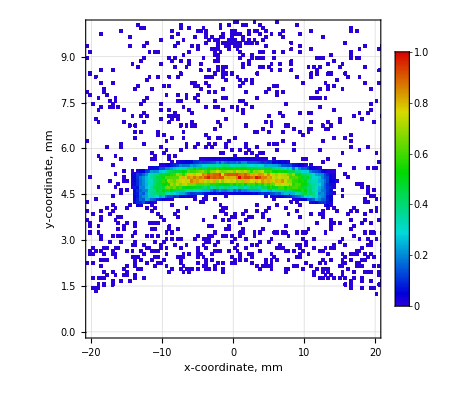
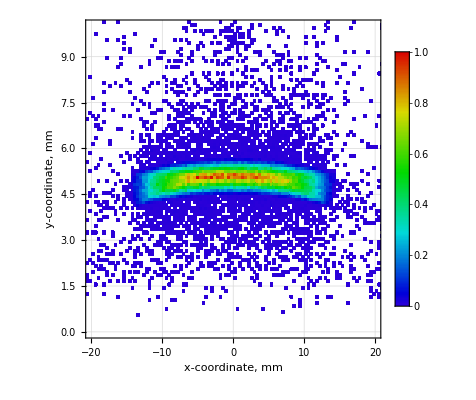
-Graphics- | -Graphics-

```mathematica
Grid[{{
DensityHistogram[detpts@res3d1000[[1]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","y-coordinate, mm"})],
DensityHistogram[detpts@res3d1000[[5]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","y-coordinate, mm"})]
}},Spacings->{2,2}]
```

```mathematica
Export["C:\\Users\\simply_nicky\\Desktop\\fig2.svg",Grid[{{
DensityHistogram[detpts@res3d1000[[1]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","y-coordinate, mm"})],
DensityHistogram[detpts@res3d1000[[5]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","y-coordinate, mm"})]
}},Spacings->{2,2}]]
```

```mathematica
Export["C:\\Users\\simply_nicky\\Desktop\\fig2_1.svg",DensityHistogram[detpts@res3d1000[[1]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-координата, мм","z-координата, мм"})]]
Export["C:\\Users\\simply_nicky\\Desktop\\fig2_2.svg",DensityHistogram[detpts@res3d1000[[5]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-координата, мм","z-координата, мм"})]]
```

```mathematica
Export["C:\\Users\\simply_nicky\\Desktop\\fig2_1.svg",DensityHistogram[detpts@res3d1000[[1]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","z-coordinate, mm"})]]
Export["C:\\Users\\simply_nicky\\Desktop\\fig2_2.svg",DensityHistogram[detpts@res3d1000[[5]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black]],FrameLabel->(Style[#,Black,24,Italic]&/@{"x-coordinate, mm","z-coordinate, mm"})]]
```

C:\Users\simply_nicky\Desktop\fig2_1.svg

C:\Users\simply_nicky\Desktop\fig2_2.svg

```mathematica
res3d1000=Import[NotebookDirectory[]<>"RMSHeight_Series_3D_1000.mx"];
res3d2000=Import[NotebookDirectory[]<>"RMSHeight_Series_3D_2000.mx"];
res3d1500=Import[NotebookDirectory[]<>"RMSHeight_Series_3D_1500.mx"];
```

```mathematica
res3d1000sph=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1000_sph.mx"];
res3d1500sph=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_1500_sph.mx"];
res3d2000sph=Import[NotebookDirectory[]<>"results/RMSHeight_Series_3D_2000_sph.mx"];
```

```mathematica
rmsh=Range[0,1.35,0.15];
```

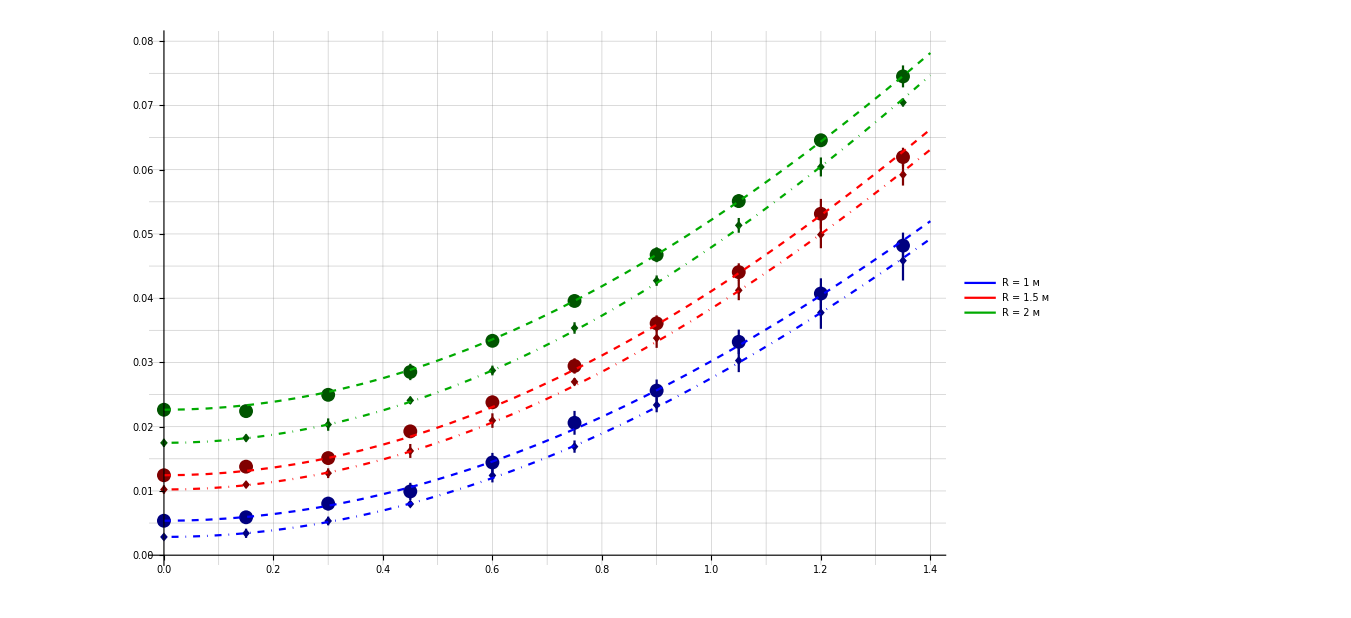
-Graphics-среднеквадратичная высота, нмдоля фонового излучения

```mathematica
Needs["ErrorBarPlots`"]
Labeled[
Show[
MapThread[Function[{res,res2,r,col},
{
ErrorListPlot[Transpose[{bckgrd[res,r,rmsh],ErrorBar/@error[res,r]}],PlotRange->{{0,1.4},{0,0.08}},GridLines->All,PlotStyle->Directive[PointSize[0.01],Darker[col,0.5]]],
ErrorListPlot[Transpose[{bckgrd[res2,r,rmsh],ErrorBar/@(1.5error[res2,r])}],PlotStyle->Directive[PointSize[0.01],Darker[col,0.5]]]/.{Point[pts_List]:>(Parallelogram[{#[[1]],#[[2]]-0.0007},{{-0.007,0.0007},{0.007,0.0007}}]&/@pts)},
ListPlot[Transpose[{#,fitmodel[res,r,rmsh]/@#}]&@Range[0,1.4,0.04],Joined->True,PlotStyle->Directive[col,Dashed]],
ListPlot[Transpose[{#,fitmodel[res2,r,rmsh]/@#}]&@Range[0,1.4,0.04],Joined->True,PlotStyle->Directive[col,DotDashed]]
}],{{res3d1000,res3d1500,res3d2000},{res3d1000sph,res3d1500sph,res3d2000sph},{r,1.5r,2r},{Blue,Red,Darker[Green]}}],
Plot[1,{x,0,1},PlotLegends->Placed[LineLegend[{Blue,Red,Darker[Green]},Style[#,Black,32,Italic]&/@{"R = 1 м","R = 1.5 м","R = 2 м"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&),LegendMarkers->Automatic],{0.2,0.8}]]
,TicksStyle->Directive[32,Black],ImageSize->1000],
(Style[#,Black,34,Italic,FontFamily->"Arabic Transparent"]&/@{"среднеквадратичная высота, нм","доля фонового излучения"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]
```

```mathematica
Export["C:\\Users\\simply_nicky\\Desktop\\fig3.svg",Labeled[
Show[
MapThread[Function[{res,res2,r,col},
{
ErrorListPlot[Transpose[{bckgrd[res,r,rmsh],ErrorBar/@error[res,r]}],PlotRange->{{0,1.4},{0,0.08}},GridLines->All,PlotStyle->Directive[PointSize[0.01],Darker[col,0.5]]],
ErrorListPlot[Transpose[{bckgrd[res2,r,rmsh],ErrorBar/@(1.5error[res2,r])}],PlotStyle->Directive[PointSize[0.01],Darker[col,0.5]]]/.{Point[pts_List]:>(Parallelogram[{#[[1]],#[[2]]-0.0007},{{-0.007,0.0007},{0.007,0.0007}}]&/@pts)},
ListPlot[Transpose[{#,fitmodel[res,r,rmsh]/@#}]&@Range[0,1.4,0.04],Joined->True,PlotStyle->Directive[col,Dashed]],
ListPlot[Transpose[{#,fitmodel[res2,r,rmsh]/@#}]&@Range[0,1.4,0.04],Joined->True,PlotStyle->Directive[col,DotDashed]]
}],{{res3d1000,res3d1500,res3d2000},{res3d1000sph,res3d1500sph,res3d2000sph},{r,1.5r,2r},{Blue,Red,Darker[Green]}}],
Plot[1,{x,0,1},PlotLegends->Placed[LineLegend[{Blue,Red,Darker[Green]},Style[#,Black,32,Italic]&/@{"R = 1 m","R = 1.5 m","R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&),LegendMarkers->Automatic],{0.2,0.8}]]
,TicksStyle->Directive[32,Black],ImageSize->1000],
(Style[#,Black,34,Italic,FontFamily->"Arabic Transparent"]&/@{"RMS roughness, nm","background signal fraction"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]]
```

C:\Users\simply_nicky\Desktop\fig3.svg

```mathematica
Rspec[θ_,σ_,ψ_]:=Exp[-((4π σ Sin[θ])/λ0)^2 ψ/(2θ)]
```

```mathematica
pow[res_,rmsh_]:=pow[res,rmsh]=Transpose[{rmsh,Length/@res/Length@res[[1]]}]
powspec[res_,rmsh_]:=powspec[res,rmsh]=Transpose[{rmsh,Length/@(resspec/@res)/Length@res[[1]]}]
errpowspec[res_]:=errpowspec[res]=1.5StandardDeviation[Length/@(resspec/@#)/Length@#[[1]]&/@Transpose[Partition[#,Quotient[Length[#],8]]&/@res]]
```

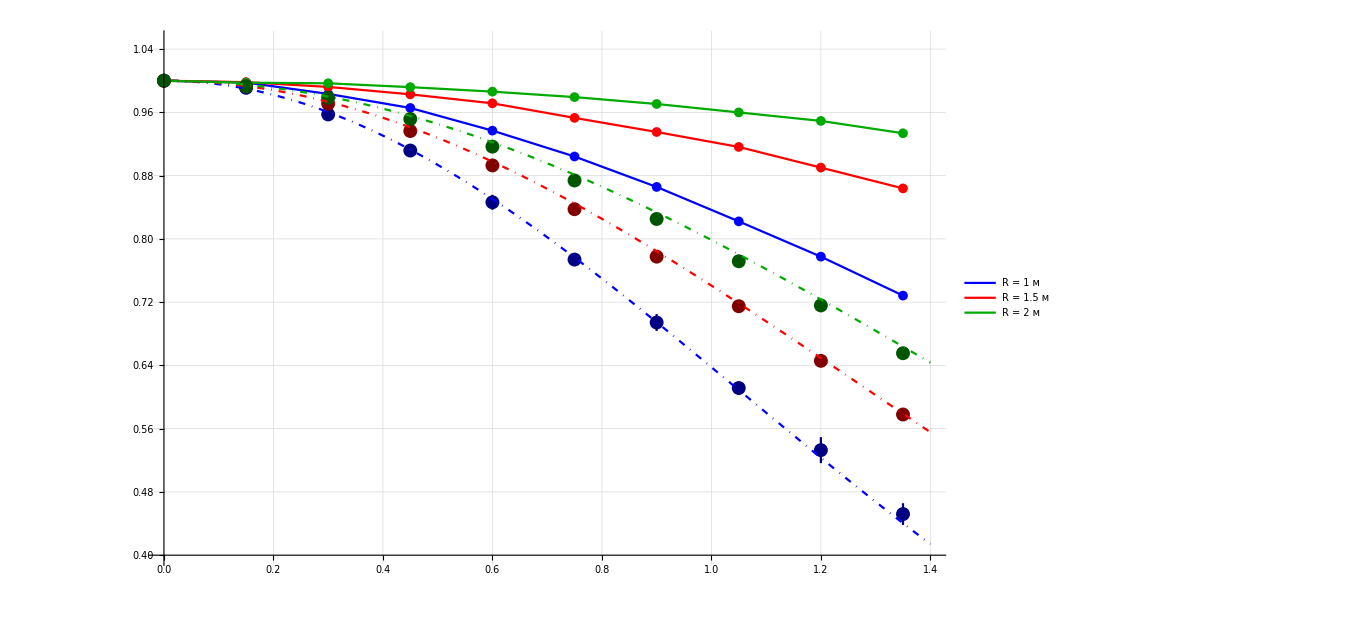
-Graphics-среднеквадратичная высота, нмэффективность поворота пучка

```mathematica
Needs["ErrorBarPlots`"]
Labeled[
Show[
MapThread[ListPlot[pow[#1,rmsh],Joined->True,PlotRange->{{0,1.4},{0.4,1.05}},PlotStyle->Directive[#2],PlotMarkers->{Automatic,10},GridLines->Full]&,{{res3d1000sph,res3d1500sph,res3d2000sph},{Blue,Red,Darker[Green]}}],
MapThread[ErrorListPlot[Transpose[{powspec[#1,rmsh],ErrorBar/@(4errpowspec[#1])}],PlotStyle->Directive[Darker[#2,0.5],PointSize[0.01]]]&,{{res3d1000sph,res3d1500sph,res3d2000sph},{Blue,Red,Darker[Green]}}],
MapThread[Plot[Rspec[2/3θ0,x,2ArcSin[d/2/#1]],{x,0,1.4},PlotStyle->Directive[#2,DotDashed]]&,{{r,1.5r,2r},{Blue,Red,Darker[Green]}}],
Plot[2,{x,0,1},PlotLegends->Placed[LineLegend[{Blue,Red,Darker[Green]},Style[#,Black,32,Italic]&/@{"R = 1 м","R = 1.5 м","R = 2 м"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&),LegendMarkers->Automatic],{0.2,0.2}]],
TicksStyle->Directive[32,Black],ImageSize->1000,AxesOrigin->{0,0.4}],
(Style[#,Black,34,Italic,FontFamily->"Arabic Transparent"]&/@{"среднеквадратичная высота, нм","эффективность поворота пучка"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]
```

```mathematica
Export["C:\\Users\\simply_nicky\\Desktop\\fig4.svg",Labeled[
Show[
MapThread[ListPlot[pow[#1,rmsh],Joined->True,PlotRange->{{0,1.4},{0.4,1.05}},PlotStyle->Directive[#2],PlotMarkers->{Automatic,10},GridLines->Full]&,{{res3d1000sph,res3d1500sph,res3d2000sph},{Blue,Red,Darker[Green]}}],
MapThread[ErrorListPlot[Transpose[{powspec[#1,rmsh],ErrorBar/@(4errpowspec[#1])}],PlotStyle->Directive[Darker[#2,0.5],PointSize[0.01]]]&,{{res3d1000sph,res3d1500sph,res3d2000sph},{Blue,Red,Darker[Green]}}],
MapThread[Plot[Rspec[2/3θ0,x,2ArcSin[d/2/#1]],{x,0,1.4},PlotStyle->Directive[#2,DotDashed]]&,{{r,1.5r,2r},{Blue,Red,Darker[Green]}}],
Plot[2,{x,0,1},PlotLegends->Placed[LineLegend[{Blue,Red,Darker[Green]},Style[#,Black,32,Italic]&/@{"R = 1 m","R = 1.5 m","R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&),LegendMarkers->Automatic],{0.2,0.2}]],
TicksStyle->Directive[32,Black],ImageSize->1000,AxesOrigin->{0,0.4}],
(Style[#,Black,34,Italic,FontFamily->"Arabic Transparent"]&/@{"RMS roughness, nm","mirror efficiency"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]]
```

C:\Users\simply_nicky\Desktop\fig4.svg

```mathematica
err1000=3StandardDeviation[Length[resspec@#]/Length@#&/@Partition[#,Quotient[Length[#],8]]]&/@res3d1000;
err1500=6StandardDeviation[Length[resspec@#]/Length@#&/@Partition[#,Quotient[Length[#],8]]]&/@res3d1500;
err2000=10StandardDeviation[Length[resspec@#]/Length@#&/@Partition[#,Quotient[Length[#],8]]]&/@res3d2000;
```

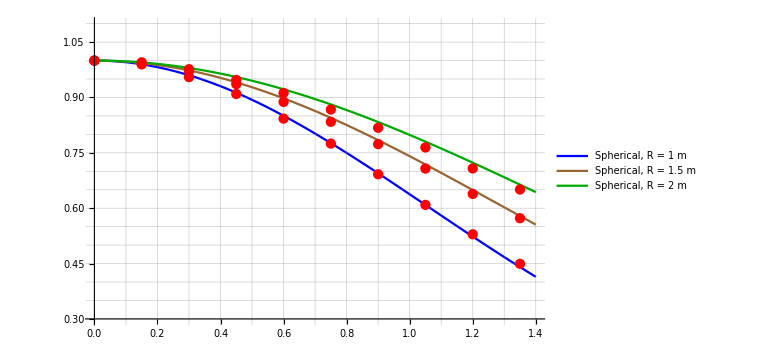
-Graphics-root-mean-square height, nmOutput specular reflectivity

```mathematica
Needs["ErrorBarPlots`"]
Grid[{{
(*Graphics[Text[Style["a)",18,Bold,Black],Scaled[{0,70}]],ImageSize->{30,400}],*)
Labeled[
Show[{
Plot[Rspec[2/3θ0,x,2ArcSin[d/(2r)]],{x,0,1.4},PlotStyle->Blue,GridLines->All,PlotRange->{{0,1.4},{0.3,1.1}},PlotLegends->Placed[LineLegend[{Blue,Brown,Darker[Green]},Style[#,Black,18,Bold]&/@{"Spherical, R = 1 m","Spherical, R = 1.5 m","Spherical, R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.3}]],ErrorListPlot[Transpose[{Transpose[{rmsh,Length/@(resspec/@res3d1000)/Length@res3d1000[[1]]}],ErrorBar/@err1000}],PlotStyle->Red],
Plot[Rspec[2/3θ0,x,2ArcSin[d/(3r)]],{x,0,1.4},PlotStyle->Brown],
ErrorListPlot[Transpose[{Transpose[{Range[0,1.35,0.15],Length/@(resspec/@res3d1500)/Length@res3d1500[[1]]}],ErrorBar/@err1500}],PlotStyle->Red],
Plot[Rspec[2/3θ0,x,2ArcSin[d/(4r)]],{x,0,1.4},PlotStyle->Darker[Green]],
ErrorListPlot[Transpose[{Transpose[{rmsh,Length/@(resspec/@res3d2000)/Length@res3d2000[[1]]}],ErrorBar/@err2000}],PlotStyle->Red]
},AxesStyle->Bold,TicksStyle->Directive[18,Black,Bold],ImageSize->Large],
(Style[#,Black,20,Bold,FontFamily->"Arabic Transparent"]&/@{"root-mean-square height, nm","Output specular reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]
}}]
```

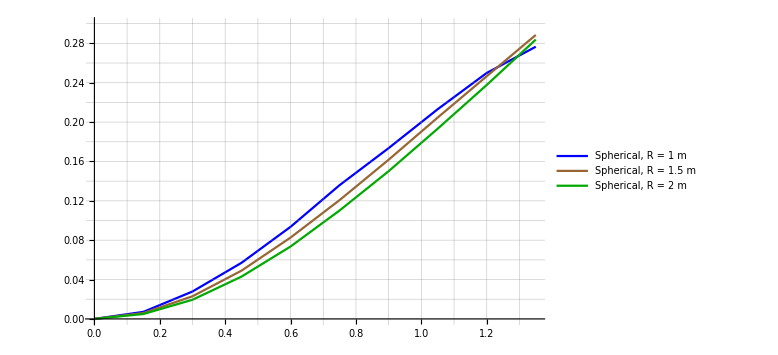
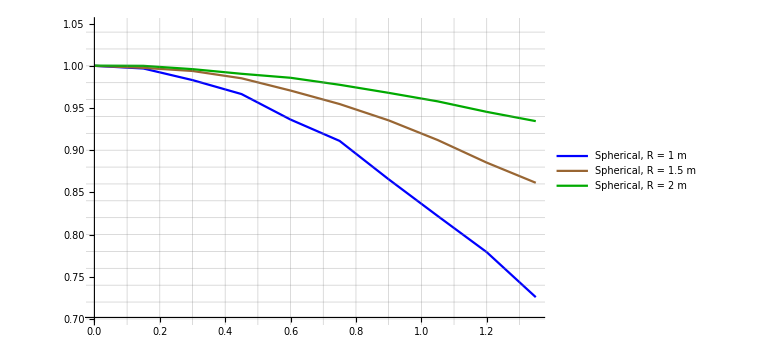
-Graphics- | -Graphics-
-Graphics-root-mean-square height, nmOutput scattered reflectivity | -Graphics-root-mean-square height, nmOutput total reflectivity

```mathematica
Grid[{{
Graphics[Text[Style["b)",22,Bold,Black],Scaled[{-70,0}]],ImageSize->{600,30}],
Graphics[Text[Style["c)",22,Bold,Black],Scaled[{-70,0}]],ImageSize->{600,30}]
},
{
Labeled[ListPlot[Transpose[{Range[0,1.35,0.15],Sort[Length/@(resscat/@#)/Length@#[[1]],Less]}]&/@{res3d1000,res3d1500,res3d2000},PlotStyle->{Blue,Brown,Darker[Green]},Joined->True,AxesStyle->Bold,TicksStyle->Directive[18,Black,Bold],ImageSize->Large,GridLines->All,PlotRange->{{0,1.35},{0,0.3}},PlotLegends->Placed[LineLegend[{Blue,Brown,Darker[Green]},Style[#,Black,18,Bold]&/@{"Spherical, R = 1 m","Spherical, R = 1.5 m","Spherical, R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.7}]],(Style[#,Black,20,Bold,FontFamily->"Arabic Transparent"]&/@{"root-mean-square height, nm","Output scattered reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4],
Labeled[ListPlot[Transpose[{Range[0,1.35,0.15],Sort[Length/@#/Length@#[[1]],Greater]}]&/@{res3d1000,res3d1500,res3d2000},PlotStyle->{Blue,Brown,Darker[Green]},Joined->True,AxesStyle->Bold,TicksStyle->Directive[18,Black,Bold],ImageSize->Large,GridLines->All,PlotRange->{{0,1.35},{0.7,1.05}},PlotLegends->Placed[LineLegend[{Blue,Brown,Darker[Green]},Style[#,Black,18,Bold]&/@{"Spherical, R = 1 m","Spherical, R = 1.5 m","Spherical, R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.3}]],(Style[#,Black,20,Bold,FontFamily->"Arabic Transparent"]&/@{"root-mean-square height, nm","Output total reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]
}},Spacings->{3,0}]
```

```mathematica
Grid[{
{Labeled[ListPlot[Transpose[{Range[0,1.35,0.15],Sort[Length/@(resscat/@#)/Length@#[[1]],Less]}]&/@{res3d1000,res3d1500,res3d2000},PlotStyle->{Blue,Brown,Darker[Green]},Joined->True,AxesStyle->Bold,TicksStyle->Directive[24,Black,Bold],ImageSize->Large,GridLines->All,PlotRange->{{0,1.35},{0,0.3}},PlotLegends->Placed[LineLegend[{Blue,Brown,Darker[Green]},Style[#,Black,20,Bold]&/@{"Spherical, R = 1 m","Spherical, R = 1.5 m","Spherical, R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.7}]],(Style[#,Black,24,Bold,FontFamily->"Arabic Transparent"]&/@{"Output scattered reflectivity"}),{Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]},
{Labeled[ListPlot[Transpose[{Range[0,1.35,0.15],Sort[Length/@#/Length@#[[1]],Greater]}]&/@{res3d1000,res3d1500,res3d2000},PlotStyle->{Blue,Brown,Darker[Green]},Joined->True,AxesStyle->Bold,TicksStyle->Directive[24,Black,Bold],ImageSize->Large,GridLines->All,PlotRange->{{0,1.35},{0.7,1.05}},PlotLegends->Placed[LineLegend[{Blue,Brown,Darker[Green]},Style[#,Black,20,Bold]&/@{"Spherical, R = 1 m","Spherical, R = 1.5 m","Spherical, R = 2 m"},LegendFunction->(Framed[#,FrameStyle->Black,Background->White]&)],{0.3,0.3}]],(Style[#,Black,24,Bold,FontFamily->"Arabic Transparent"]&/@{"root-mean-square height, nm","Output total reflectivity"}),{Bottom,Left},RotateLabel->True,ImageMargins->4,FrameMargins->4]}
}]
```

-Graphics-Output scattered reflectivity
-Graphics-root-mean-square height, nmOutput total reflectivity

```mathematica
res3dsph=Import[NotebookDirectory[]<>"RMSHeight_Series_Sph3D.mx"];
```

```mathematica
Export["",Grid[{
{
Graphics[Text[Style["a)",22,Bold,Black],Scaled[{-70,0}]],ImageSize->{500,30}],
Graphics[Text[Style["b)",22,Bold,Black],Scaled[{-70,0}]],ImageSize->{500,30}]
},
{
DensityHistogram[detpts@res3dsph[[1]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22,Bold],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black,Bold]],FrameLabel->(Style[#,Black,24,Bold]&/@{"x-coordinate, mm","y-coordinate, mm"})],
DensityHistogram[detpts@res3dsph[[5]],{{0.4},{0.1}},ColorFunction->(Hue[0.7(1-#),1,0.85]&),ImageSize->400,PlotRange->{{-20,20},{0,10}},FrameTicksStyle->Directive[Black,22,Bold],GridLines->All,ChartLegends->BarLegend[{(Hue[0.7(1-#),1,0.85]&),{0,1}},LabelStyle->Directive[22
,Black,Bold]],FrameLabel->(Style[#,Black,24,Bold]&/@{"x-coordinate, mm","y-coordinate, mm"})]
}
},Spacings->{2,2}]]
```